```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(*Inferred root height for μ = 3 x10^-5*)
```

```mathematica
path="Path_to_directory\\Fasta files\\stats\\stats_epistasis\\nexformat_m5_";(*change the directory here*)
dataX={1000,10000,100000,1000000,10000000};(*time window of rate measurement, T^**)
(*every 202 lines in the log file corresponds to a single *converged* BEAST run with the last 2 million steps (out of 10 million steps)*)
(*to collect the inferred root heights from log file, we subtract the entries in treeModel.rootHeight from the the time window of rate measurement, T^**)
dataY5={Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-1000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-100000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-1000000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10000000};
(*error bars represent the interquantile range*)
error5down={Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-1000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-100000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-1000000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10000000};
error5up={Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-1000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-100000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-1000000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10000000};
errorH5=error5up;
errorL5=error5down;
f[y_]:=Transpose[{dataX,y}];
```

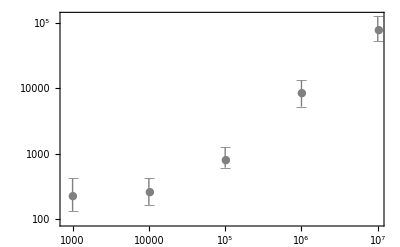

```mathematica
plot5root=ListLogLogPlot[{f[errorL5],f[errorH5],f[dataY5]},Filling->{1->{2}},Joined->False,PlotStyle->{Gray},PlotMarkers->{" —"," —"," ●"},PlotTheme->"Detailed",FillingStyle->Gray,PlotRange->All]
```

```mathematica
(*Inferred substitution rate for μ = 3 x10^-5*)
```

```mathematica
path="Path_to_directory\\Fasta files\\stats\\stats_epistasis\\median_list_m5_";(*change the directory here*)(*collecting the inferred median clock rate from 100 independent simulation runs*)
dataX={1000,10000,100000,1000000,10000000};dataY5={Median[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]]]};
(*error bars represent the interquantile range*)
error5down={Quantile[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]],1/4]};
error5up={Quantile[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]],3/4]};
errorH5=error5up;
errorL5=error5down;
f[y_]:=Transpose[{dataX,y}];
```

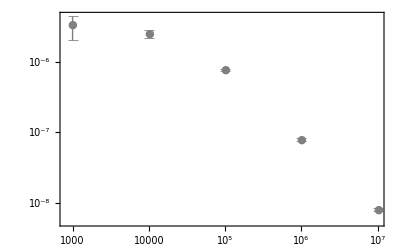

```mathematica
plot5=ListLogLogPlot[{f[errorL5],f[errorH5],f[dataY5]},Filling->{1->{2}},Joined->False,PlotStyle->{Gray},PlotMarkers->{" —"," —"," ●"},PlotTheme->"Detailed",FillingStyle->Gray,PlotRange->All]
```

```mathematica
(*Estimated substitution rate according to the PoW transformation*)
```

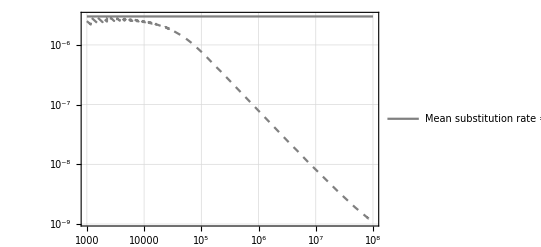

```mathematica
μ=3 10^-5;(*total substitution rate per site*)
μN=μ/3;(*substitution rate per nucleotide*)
n=100;  (*effective population size*)
α=3/4;(*saturation frequency*)
L1=100;(*number of neutral sites*)
L2=900;(*number of compensatory doublets*)
T=2n;(*Estimated TMRCA. In the absence of biased root height estimation, T=2 Subscript[N, e]*)
theory5=LogLogPlot[{.1μ+.9 3 μN^2,(N[-α (Log[1-(Floor[α(1-E^(-μ (t+2n)/α))*L1+α(1-E^(-3 μN^2(t+2n)/α))*L2])/((L1+L2)α)])]/.∞->4.9)/(t+T)},{t,1000,10^8},PlotRange->All,PlotLegends->{"Mean substitution rate = 3×10^-6"},PlotStyle->{{Gray,Thick},{Dashed,Gray}},LabelStyle->Directive[Black,16],PlotTheme->"Detailed"]
```

```mathematica
(*Inferred root height for μ = 3 x10^-4*)
```

```mathematica
path="Path_to_directory\\Fasta files\\stats\\stats_epistasis\\nexformat_m4_";(*change the directory here*)
dataX={100,1000,10000,100000,1000000,10000000};(*time window of rate measurement, T^**)
(*every 202 lines in the log file corresponds to a single *converged* BEAST run with the last 2 million steps (out of 10 million steps)*)
(*to collect the inferred root heights from log file, we subtract the entries in treeModel.rootHeight from the the time window of rate measurement, T^**)
dataY4={Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-100,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-1000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-100000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-1000000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10000000};
(*error bars represent the interquantile range*)
error4down={Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-100,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-1000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-100000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-1000000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10000000};
error4up={Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-100,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-1000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-100000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-1000000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10000000};
errorH4=error4up;
errorL4=error4down;
f[y_]:=Transpose[{dataX,y}];
```

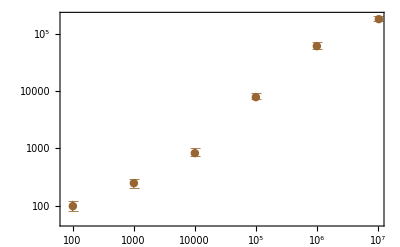

```mathematica
plot4root=ListLogLogPlot[{f[errorL4],f[errorH4],f[dataY4]},Filling->{1->{2}},Joined->False,PlotStyle->{Brown},PlotMarkers->{" —"," —"," ●"},PlotTheme->"Detailed",FillingStyle->Brown,PlotRange->All]
```

```mathematica
(*Inferred substitution rate for μ = 3 x10^-4*)
```

```mathematica
path="Path_to_directory\\Fasta files\\stats\\stats_epistasis\\median_list_m4_";
dataX={100,1000,10000,100000,1000000,10000000};
dataY4={Median[Flatten[Import[StringJoin[path,"100.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]]]};
(*error bars represent the interquantile range*)
error4down={Quantile[Flatten[Import[StringJoin[path,"100.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]],1/4]};
error4up={Quantile[Flatten[Import[StringJoin[path,"100.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]],3/4]};
errorH4=error4up;
errorL4=error4down;
f[y_]:=Transpose[{dataX,y}];
```

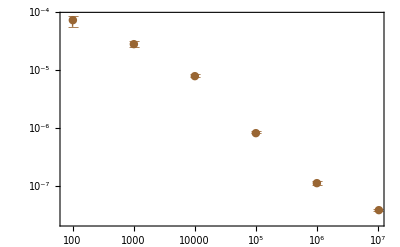

```mathematica
plot4=ListLogLogPlot[{f[errorL4],f[errorH4],f[dataY4]},Filling->{1->{2}},Joined->False,PlotStyle->{Brown},PlotMarkers->{" —"," —"," ●"},PlotTheme->"Detailed",FillingStyle->Brown,PlotRange->All]
```

```mathematica
(*Estimated substitution rate according to the PoW transformation*)
```

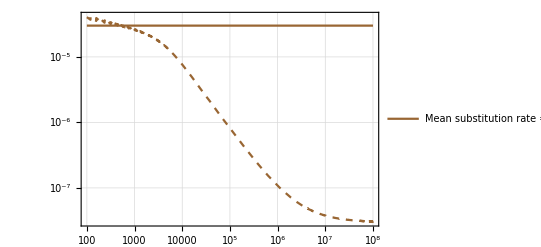

```mathematica
μ=3 10^-4;(*total substitution rate per site*)
μN=μ/3;(*substitution rate per nucleotide*)
n=100;  (*effective population size*)
α=3/4;(*saturation frequency*)
L1=100;(*number of neutral sites*)
L2=900;(*number of compensatory doublets*)
T=99;(*Estimated TMRCA. In the absence of biased root height estimation, T=2 Subscript[N, e]*)
theory4=LogLogPlot[{.1μ+.9 3 μN^2,(N[-α (Log[1-(Floor[α(1-E^(-μ (t+2n)/α))*L1+α(1-E^(-3 μN^2(t+2n)/α))*L2])/((L1+L2)α)])]/.∞->4.9)/(t+T)},{t,100,10^8},PlotRange->All,PlotLegends->{"Mean substitution rate = 3×10^-5"},PlotStyle->{{Brown,Thick},{Dashed,Brown}},LabelStyle->Directive[Black,16],PlotTheme->"Detailed"]
```

```mathematica
(*Inferred root height for μ = 3 x10^-3*)
```

```mathematica
path="Path_to_directory\\Fasta files\\stats\\stats_epistasis\\nexformat_m3_";(*change the directory here*)
dataX={10,100,1000,10000,100000,1000000,10000000};(*time window of rate measurement, T^**)
(*every 202 lines in the log file corresponds to a single *converged* BEAST run with the last 2 million steps (out of 10 million steps)*)
(*to collect the inferred root heights from log file, we subtract the entries in treeModel.rootHeight from the the time window of rate measurement, T^**)
dataY3={Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-100,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-1000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-100000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-1000000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10000000};
(*error bars represent the interquantile range*)
error3down={Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-100,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-1000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-100000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-1000000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10000000};
error3up={Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-100,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-1000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-100000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-1000000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10000000};
errorH3=error3up;
errorL3=error3down;
f[y_]:=Transpose[{dataX,y}];
```

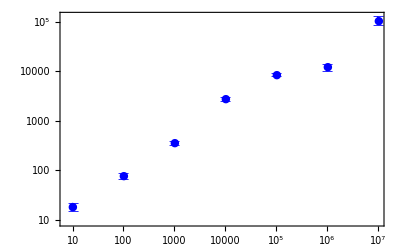

```mathematica
plot3root=ListLogLogPlot[{f[errorL3],f[errorH3],f[dataY3]},Filling->{1->{2}},Joined->False,PlotStyle->{Blue},PlotMarkers->{" —"," —"," ●"},PlotTheme->"Detailed",FillingStyle->Blue,PlotRange->All]
```

```mathematica
path="Path_to_directory\\Fasta files\\stats\\stats_epistasis\\median_list_m3_";(*change the directory here*)
dataX={10,100,1000,10000,100000,1000000,10000000};
dataY3={Median[Flatten[Import[StringJoin[path,"10.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"100.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]]]};
(*error bars represent the interquantile range*)
error3down={Quantile[Flatten[Import[StringJoin[path,"10.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"100.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]],1/4]};
error3up={Quantile[Flatten[Import[StringJoin[path,"10.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"100.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"1000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"10000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]],3/4]};
errorH3=error3up;
errorL3=error3down;
f[y_]:=Transpose[{dataX,y}];
```

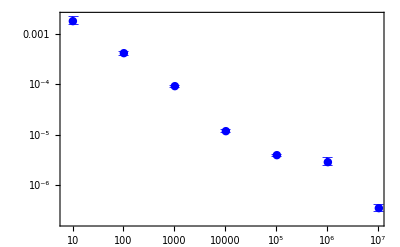

```mathematica
plot3=ListLogLogPlot[{f[errorL3],f[errorH3],f[dataY3]},Filling->{1->{2}},Joined->False,PlotStyle->{Blue},PlotMarkers->{" —"," —"," ●"},PlotTheme->"Detailed",FillingStyle->Blue,PlotRange->All]
```

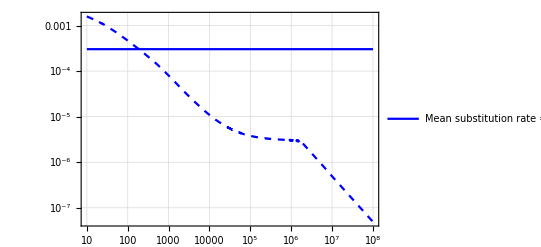

```mathematica
μ=3 10^-3;(*total substitution rate per site*)
μN=μ/3;(*substitution rate per nucleotide*)
n=100;  (*effective population size*)
α=3/4;(*saturation frequency*)
L1=100;(*number of neutral sites*)
L2=900;(*number of compensatory doublets*)
T=18;(*Estimated TMRCA. In the absence of biased root height estimation, T=2 Subscript[N, e]*)
theory3=LogLogPlot[{.1μ+.9 3 μN^2,(N[-α (Log[1-(Floor[α(1-E^(-μ (t+2n)/α))*L1+α(1-E^(-3 μN^2(t+2n)/α))*L2])/((L1+L2)α)])]/.∞->4.9)/(t+T)},{t,10,10^8},PlotRange->All,PlotLegends->{"Mean substitution rate = 3×10^-4"},PlotStyle->{{Blue,Thick},{Dashed,Blue}},LabelStyle->Directive[Black,16],PlotTheme->"Detailed"]
```

```mathematica
(*Inferred root height for μ = 3 x10^-2*)
```

```mathematica
path="Path_to_directory\\Fasta files\\stats\\stats_epistasis\\nexformat_m2_";(*change the directory here*)
(*remove any simulation runs that are not yet converged after 2 million steps for T^*=100, 1000, 10000*)
pos100={};
pos1000={};
pos10000={};
logs100=Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]];
sel=Select[Transpose[logs100][[-5]],#<1 10^-2&];
For[o=1,o≤Length[sel],o++,AppendTo[pos100,Position[Transpose[logs100][[-5]],sel⟦o⟧]⟦1,1⟧]];
logs1000=Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]];
sel=Select[Transpose[logs1000][[-5]],#<1 10^-3&];
For[o=1,o≤Length[sel],o++,AppendTo[pos1000,Position[Transpose[logs1000][[-5]],sel⟦o⟧]⟦1,1⟧]];
logs10000=Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]];
sel=Select[Transpose[logs10000][[-5]],#<1 10^-3&];
For[o=1,o≤Length[sel],o++,AppendTo[pos10000,Position[Transpose[logs10000][[-5]],sel⟦o⟧]⟦1,1⟧]];
path="C:\\Users\\ghafa\\Desktop\\University related\\University of Oxford\\Wroks with Aris\\Paper1\\stats\\stats_epistasis\\nexformat_m2_";(*change the directory here*)
dataX={10,100,1000,10000,100000,1000000,10000000};(*time window of rate measurement, T^**)
(*every 202 lines in the log file corresponds to a single *converged* BEAST run with the last 2 million steps (out of 10 million steps)*)
(*to collect the inferred root heights from log file, we subtract the entries in treeModel.rootHeight from the the time window of rate measurement, T^**)
dataY2={Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10,Median[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]][[pos100]]]-100,
Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]][[pos1000]],202]}]]-1000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]][[pos10000]],202]}]]-10000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-100000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-1000000,Median[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}]]-10000000};
(*error bars represent the interquantile range*)
error2down={Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10,Quantile[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]][[pos100]],1/4]-100,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]][[pos1000]],202]}],1/4]-1000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]][[pos10000]],202]}],1/4]-10000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-100000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-1000000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],1/4]-10000000};
error2up={Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10,Quantile[Transpose[Import[StringJoin[path,"100.log.txt"],"Data"][[2;;]]][[-9]][[pos100]],3/4]-100,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000.log.txt"],"Data"][[2;;]]][[-9]][[pos1000]],202]}],3/4]-1000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000.log.txt"],"Data"][[2;;]]][[-9]][[pos10000]],202]}],3/4]-10000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"100000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-100000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"1000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-1000000,Quantile[MapThread[Median,{Partition[Transpose[Import[StringJoin[path,"10000000.log.txt"],"Data"][[2;;]]][[-9]],202]}],3/4]-10000000};
errorH2=error2up;
errorL2=error2down;
f[y_]:=Transpose[{dataX,y}];
```

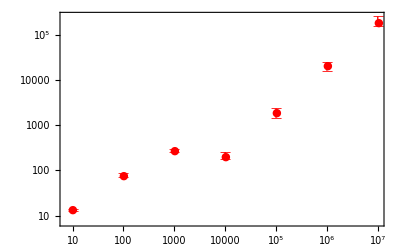

```mathematica
plot2root=ListLogLogPlot[{f[errorL2],f[errorH2],f[dataY2]},Filling->{1->{2}},Joined->False,PlotStyle->{Red},PlotMarkers->{" —"," —"," ●"},PlotTheme->"Detailed",FillingStyle->Red,PlotRange->All]
```

```mathematica
(*Inferred substitution rate for μ = 3 x10^-2*)
```

```mathematica
path="Path_to_directory\\Fasta files\\stats\\stats_epistasis\\median_list_m2_";(*change the directory here*)
dataX={10,100,1000,10000,100000,1000000,10000000};
dataY2={Median[Flatten[Import[StringJoin[path,"10.txt"],"Data"]]],Median[Select[Transpose[logs100][[-5]],#<1 10^-2&]],Median[Select[Transpose[logs1000][[-5]],#<1 10^-3&]],Median[Select[Transpose[logs10000][[-5]],#<1 10^-3&]],Median[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]]],Median[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]]]};
(*error bars represent the interquantile range*)
error2down={Quantile[Flatten[Import[StringJoin[path,"10.txt"],"Data"]],1/4],Quantile[Select[Transpose[logs100][[-5]],#<1 10^-2&],1/4],Quantile[Select[Transpose[logs1000][[-5]],#<1 10^-3&],1/4],Quantile[Select[Transpose[logs10000][[-5]],#<1 10^-3&],1/4],Quantile[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]],1/4],Quantile[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]],1/4]};
error2up={Quantile[Flatten[Import[StringJoin[path,"10.txt"],"Data"]],3/4],Quantile[Select[Transpose[logs100][[-5]],#<1 10^-2&],3/4],Quantile[Select[Transpose[logs1000][[-5]],#<1 10^-3&],3/4],Quantile[Select[Transpose[logs10000][[-5]],#<1 10^-3&],3/4],Quantile[Flatten[Import[StringJoin[path,"100000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"1000000.txt"],"Data"]],3/4],Quantile[Flatten[Import[StringJoin[path,"10000000.txt"],"Data"]],3/4]};
errorH2=error2up;
errorL2=error2down;
f[y_]:=Transpose[{dataX,y}];
```

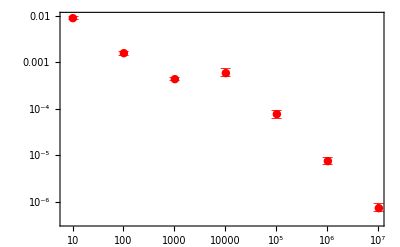

```mathematica
plot2=ListLogLogPlot[{f[errorL2],f[errorH2],f[dataY2]},Filling->{1->{2}},Joined->False,PlotStyle->{Red},PlotMarkers->{" —"," —"," ●"},PlotTheme->"Detailed",FillingStyle->Red,PlotRange->All]
```

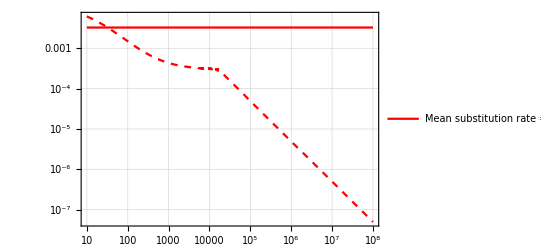

```mathematica
μ=3 10^-2;(*total substitution rate per site*)
μN=μ/3;(*substitution rate per nucleotide*)
n=100;  (*effective population size*)
α=3/4;(*saturation frequency*)
L1=100;(*number of neutral sites*)
L2=900;(*number of compensatory doublets*)
T=13;(*Estimated TMRCA. In the absence of biased root height estimation, T=2 Subscript[N, e]*)
theory2=LogLogPlot[{.1μ+.9 3 μN^2,(N[-α (Log[1-(Floor[α(1-E^(-μ (t+2n)/α))*L1+α(1-E^(-3 μN^2(t+2n)/α))*L2])/((L1+L2)α)])]/.∞->4.9)/(t+T)},{t,10,10^8},PlotRange->All,PlotLegends->{"Mean substitution rate = 3×10^-3"},PlotStyle->{{Red,Thick},{Dashed,Red}},LabelStyle->Directive[Black,16],PlotTheme->"Detailed"]
```

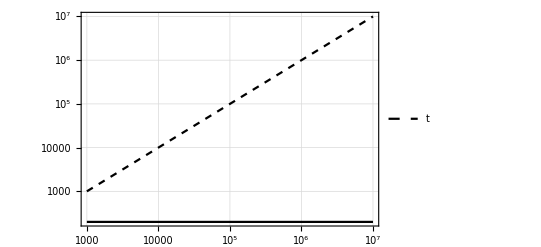

```mathematica
trend=LogLogPlot[{t,200},{t,10^3,10^7},PlotRange->All,PlotLegends->{"t"},PlotStyle->{{Dashed,Black},{Thick,Black}},LabelStyle->Directive[Black,16],PlotTheme->"Detailed"]
```

```mathematica
Show[plot5root,trend,plot4root,plot3root,plot2root,PlotRange-> {{1,18},{All,All}},FrameStyle->Directive[Black,18],FrameLabel->{"Observation time, t^* (in generations)","Estimated TMRCA of the population"},LabelStyle->Directive[Black,16],ImageSize->700]
```

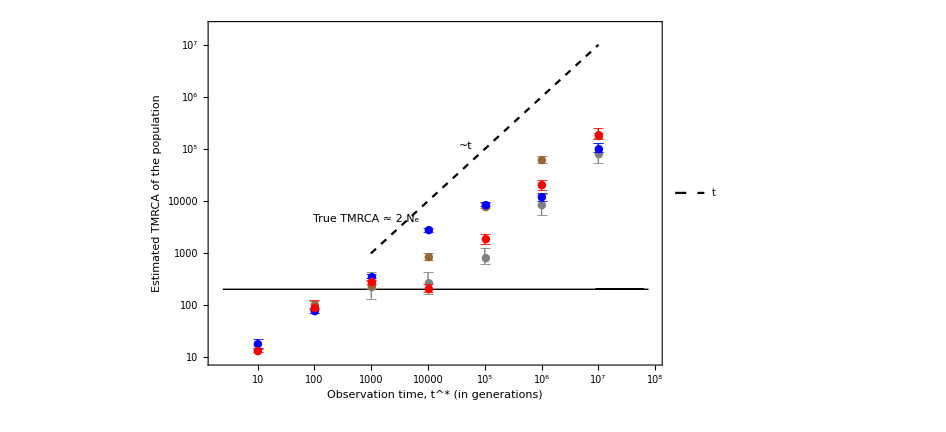

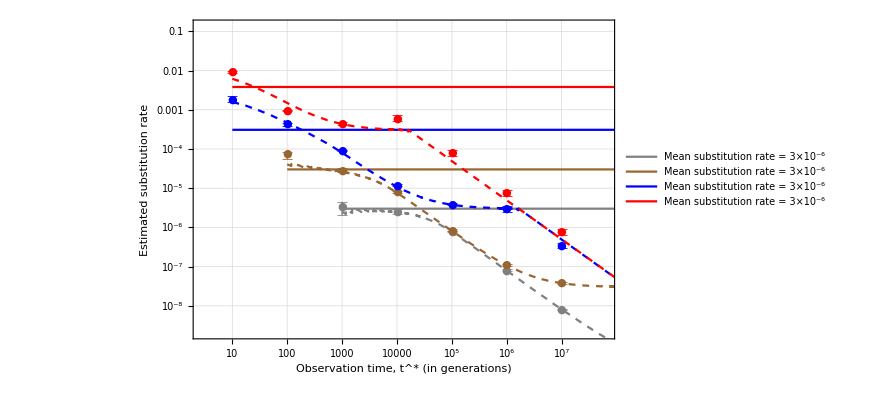

```mathematica
Show[plot5,theory5,plot4,theory4,plot3,theory3,plot2,theory2,PlotRange-> {{1,18},{-20,-2}},FrameStyle->Directive[Black,18],FrameLabel->{"Observation time, t^* (in generations)","Estimated substitution rate"},LabelStyle->Directive[Black,19],ImageSize->650]
```